```mathematica
LinguisticAssistant
```

```mathematica
Entity["MilitaryConflict","FirstPunicWar"]["Subconflicts"]
```

{Battle of Cape Ecnomus,Battle of Mylae,Battle of Agrigentum,Battle of Drepana,Battle of Messana,Battle of the Lipari Islands,Battle of Adis,Battle of Panormus,Battle of Tyndaris,Battle of Sulci,Siege of Lilybaeum,Siege of Aspis,Battle of Bagradas,Battle of the Egadi Islands}

```mathematica
GeoListPlot[%]
```

-Graphics-

```mathematica
GeoListPlot[Entity["MilitaryConflict","BattleOfAgrigentum"]]
```

-Graphics-

```mathematica
GeoElevationData/@%2
```

GeoElevationData::loc: Battle of Adis is not a valid location or pair of locations.

GeoElevationData::loc: Siege of Lilybaeum is not a valid location or pair of locations.

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],GeoElevationData[Battle of Adis],QuantityArray[…],QuantityArray[…],QuantityArray[…],GeoElevationData[Siege of Lilybaeum],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

```mathematica
Normal[%]
```

{{{275.591 ft}},{{42.6509 ft}},{{695.538 ft}},{{36.0892 ft}},{{-183.727 ft}},{{-459.318 ft}},GeoElevationData[Battle of Adis],{{78.7402 ft}},{{925.197 ft}},{{183.727 ft}},GeoElevationData[Siege of Lilybaeum],{{49.2126 ft}},{{141.076 ft}},{{-672.572 ft}}}

```mathematica
%2[[5]]
```

Battle of Messana

```mathematica
GeoNearest["Shipwreck",GeoPosition[Entity["MilitaryConflict","BattleOfMessana"]],10]
```

{Giovanni delle Bande Nere,U-374,HMS Laforey,USS PC-558,USS SC-694,HMS Thetis,F174,USS Maddox,HMS Grampus,USS Buck}

```mathematica
GeoListPlot[%]
```

-Graphics-

```mathematica
Entity["Shipwreck","HMSThetisN25::y4zbw"]
```

```mathematica
InputForm[Entity["Shipwreck","HMSThetisN25::y4zbw"]]
```

Entity["Shipwreck", "HMSThetisN25::y4zbw"]

```mathematica
InputForm[Entity["MilitaryConflict","BattleOfMessana"]]
```

Entity["MilitaryConflict", "BattleOfMessana"]

```mathematica
GeoNearest["MilitaryConflict",Entity["Shipwreck","HMSThetisN25::y4zbw"],5]
```

GeoNearest::unktype: Unknown type MilitaryConflict.

GeoNearest[MilitaryConflict,HMS Thetis,5]

```mathematica
LinguisticAssistant["Subconflicts"]
```

{Invasion of Kuwait,Highway of Death,Battle of 73 Easting,Battle of Khafji,Liberation of Kuwait,Gulf War Air Campaign,Battle of Medina Ridge,Battle of Dasman Palace,Battle of Norfolk,Persian Gulf War Air Combat,Battle of Rumaila,Package Q Airstrike,Battle of the Bridges,Battle of Al Busayyah,Battle of Phase Line Bullet,Battle of Kuwait International Airport,Battle of Bubiyan,Battle of Wadi Al-Batin,Operation Friction,Battle for Jalibah Airfield,Battle of Ad-Dawrah,Battles of Qurah and Umm al Maradim,Battle of Failaka,Safwan Airfield standoff}

```mathematica
GeoListPlot[%]
```

-Graphics-

```mathematica
LinguisticAssistant["Subconflicts"]
```

{English Civil War,Second English Civil War,Third English Civil War,Battle of the Severn}

```mathematica
Entity["MilitaryConflict","FirstEnglishCivilWar"]["Subconflicts"]
```

{Battle of Naseby,Battle of Edgehill,Battle of Marston Moor,Sieges of Taunton,Second Battle of Newbury,First Battle of Newbury,Battle of Langport,Siege of Oxford,Battle of Turnham Green,Battle of Cropredy Bridge,Battle of Roundway Down,Battle of Stow-on-the-Wold,Battle of Lansdowne,Battle of Adwalton Moor,Siege of Hull,Battle of Powick Bridge,Siege of York,Battle of Lostwithiel,Battle of Nantwich,Battle of Brentford,Bolton massacre,Siege of Gloucester,Battle of Gainsborough,Battle of Rowton Heath,Battle of Hopton Heath,Battle of Chalgrove Field,Battle of Torrington,Battle of Winceby,Battle of Camp Hill,Siege of Basing House,Battle of Cheriton,Battle of Alton,Storming of Bristol,Siege of Chester,Relief of Newark,Battle of Stratton,Siege of Lathom House,Battle of Braddock Down,Battle of Leeds,Siege of Portsmouth,Siege of Reading,Battle of Burton Bridge,Siege of Hull,Battle of Seacroft Moor,Battle of Aldbourne Chase,Siege of Bristol,Battle of Selby,Siege of Lyme Regis,Battle of Sourton Down,Battle of Ormskirk,Battle of Ripple Field,Siege of Chichester,Battle of Montgomery}

```mathematica
FindGeoLocation["1 North Parade, Oxford, UK"]
```

```mathematica
TimelinePlot[%18]
```

-Graphics-

```mathematica
GeoListPlot[%21]
```

-Graphics-

```mathematica
Entity["MilitaryConflict","BattleOfChalgroveField"]["Dataset"]
```

Dataset[<>]

```mathematica
LinguisticAssistant["Dataset"]
```

Dataset[<>]

```mathematica
Entity["MilitaryConflict","GoldBeach"]["Dataset"]
```

Dataset[<>]

```mathematica
LinguisticAssistant["Dataset"]
```

Dataset[<>]

```mathematica
GeoImage[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

```mathematica
GeoImage[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

```mathematica
GeoImage[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[LinguisticAssistant,LinguisticAssistant]],MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
GeoNearest["Park",GeoPosition[LinguisticAssistant],5]
```

{Gettysburg National Military Park,Gettysburg National Cemetery,Eisenhower National Historic Site,Catoctin Mountain Park,Monocacy National Battlefield}

```mathematica
GeoListPlot[Entity["Park","GettysburgNationalMilitaryPark"]]
```

-Graphics-

## Tides

```mathematica
Entity["MilitaryConflict","GoldBeach"]["StartDate"]
```

Day: Tue 6 Jun 1944

```mathematica
GeoPosition[Entity["MilitaryConflict","GoldBeach"]]
```

GeoPosition[{49.3453,-0.571667}]

```mathematica
TideData[GeoPosition[{49.345277777778,-0.57166666666667}],"WaterLevel",{DateObject[{1944,6,6},"Day","Gregorian",-4.]-LinguisticAssistant,DateObject[{1944,6,6},"Day","Gregorian",-4.]+LinguisticAssistant,"Hour"}]
```

Missing[NotAvailable]

```mathematica
GeoImage[GeoPosition[{49.345277777778,-0.57166666666667}],GeoRange->LinguisticAssistant]
```

-Graphics-

```mathematica
TideData[LinguisticAssistant,"WaterLevel",{DateObject[{1944,6,6},"Day","Gregorian",-4.]-LinguisticAssistant,DateObject[{1944,6,6},"Day","Gregorian",-4.]+LinguisticAssistant,"Hour"}]
```

TimeSeries[…]

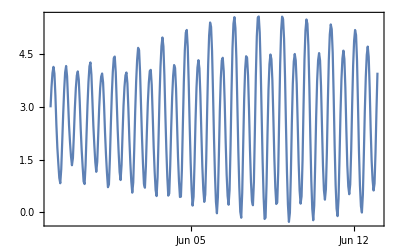

```mathematica
DateListPlot[%]
```

```mathematica
UnitConvert[Now-DateObject[{1944,6,6},"Day","Gregorian",-4.],"Years"]
```

73.3233 yr

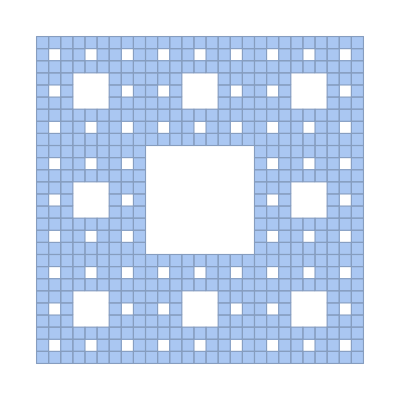

```mathematica
MengerMesh[3]
```

```mathematica
RegionIntersection[Disk[],-Graphics-]
```

BooleanRegion[#1&&#2&,{Disk[{0,0}],-Graphics-}]

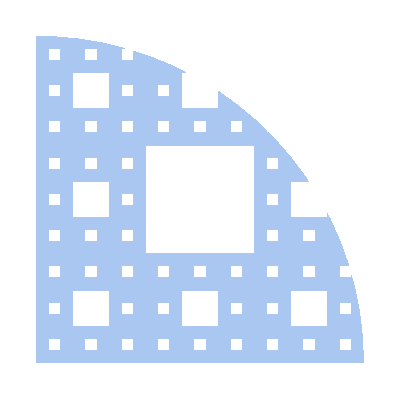

```mathematica
Region[%]
```

```mathematica
Area[%]
```

Area::nmet: Unable to compute the area of region ….

Area[-Graphics-]

```mathematica
Integrate[x^2-y^2,{x,y}∈-Graphics-]
```

0.0000102586

```mathematica
Integrate[1,{x,y}∈-Graphics-]
```

0.526929

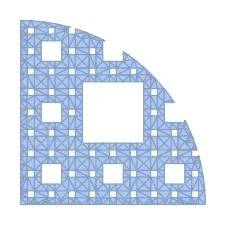

```mathematica
DiscretizeRegion[-Graphics-]
```

```mathematica
Area[%]
```

0.526929

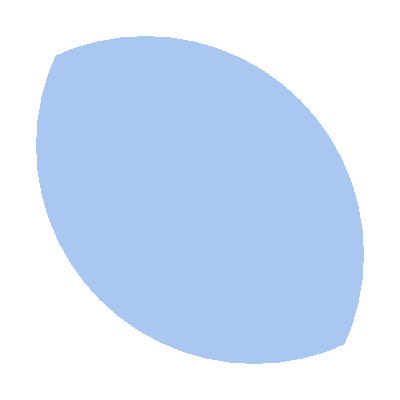

```mathematica
Region[RegionIntersection[Disk[{0,0}],Disk[{1/2,1/2}]]]
```

```mathematica
Area[%]
```

1/16 (-4 √7-√(2 (4-√7))-√(14 (4-√7))-√(2 (4+√7))+√(14 (4+√7))+16 π-16 ArcSin[1/4 (1-√7)]-16 ArcSin[1/4 (1+√7)])

```mathematica
N[%]
```

1.75742

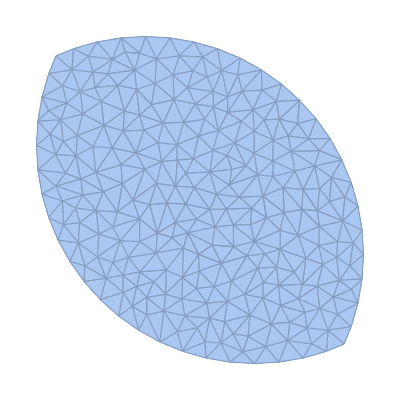

```mathematica
DiscretizeRegion[-Graphics-]
```

```mathematica
Area[%]
```

1.7523

```mathematica
Area[DiscretizeRegion[-Graphics-,PerformanceGoal->"Quality"]]
```

1.7523

```mathematica
Manipulate[DiscretizeRegion[-Graphics-,MaxCellMeasure->10^m],{m,-2,0}]
```

```mathematica
Manipulate[DiscretizeRegion[-Graphics-,MaxCellMeasure->10^m],{m,-3,0}]
```

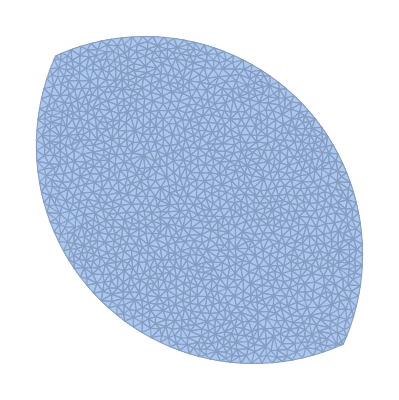
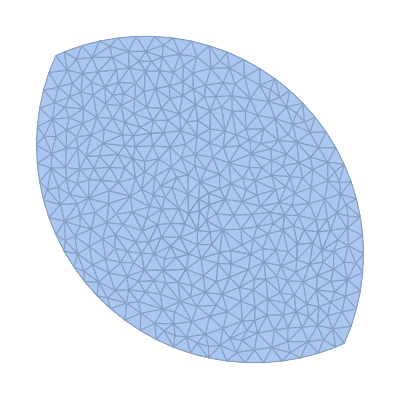
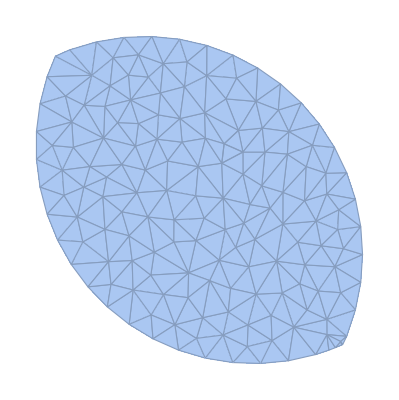
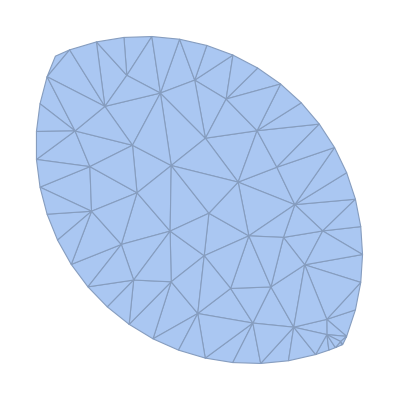
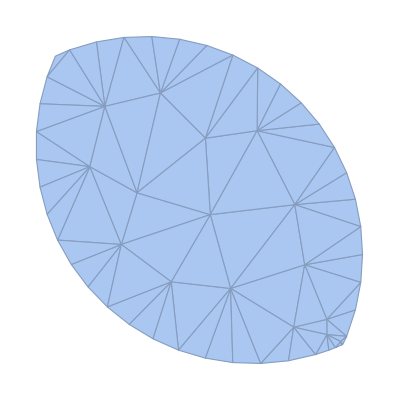
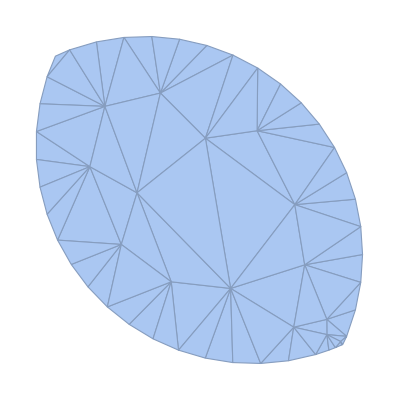
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[DiscretizeRegion[-Graphics-,MaxCellMeasure->10^m],{m,-3,0,.5}]
```

```mathematica
Area/@%
```

{1.75649,1.75451,1.75095,1.75095,1.75095,1.75095,1.75095}

```mathematica
%-%[[1]]
```

{0.,-0.00197919,-0.00554695,-0.00554695,-0.00554695,-0.00554695,-0.00554695}

```mathematica
Region[RegionIntersection[Ball[{0,0,0}],Ball[{1/2,1/2,1/2}]]]
```

-Graphics3D-

```mathematica
DiscretizeRegion[%]
```

-Graphics3D-

```mathematica
Volume[%]
```

1.63225

```mathematica
lf=LinguisticAssistant["MeshRegion"]
```

-Graphics3D-

```mathematica
rf=LinguisticAssistant["MeshRegion"]
```

-Graphics3D-

```mathematica
RegionCentroid/@{lf,rf}
```

{{92.1945,-85.0585,589.207},{-93.5209,-85.049,589.217}}

```mathematica
RegionCentroid[rf]-RegionCentroid[lf]
```

{-185.715,0.00941045,0.0094844}

```mathematica
Translate[lf,%]
```

Translate[-Graphics3D-,{-185.715,0.00941045,0.0094844}]

```mathematica
TransformedRegion[-Graphics3D-,TranslationTransform[{-185.71539825323634,0.009410445178261284,0.009484401913709917}]]
```

-Graphics3D-

```mathematica
Region[RegionUnion[-Graphics3D-,rf]]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[LinguisticAssistant]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[LinguisticAssistant,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[LinguisticAssistant,PlotTheme->"Scientific",SkinStyle->Automatic]
```

-Graphics3D-

```mathematica
LinguisticAssistant["MeshRegion"]
```

-Graphics3D-

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

```mathematica
Entity["AnatomicalStructure","MusculatureOfLeftFoot"]["Properties"]
```

{abbreviation,adjacent joint count,adjacent joints,adjacent structures,afferent vessel,anatomical groups,anatomical regions,anatomical spaces,arterial supply,articulating bones,associated cerebral lobe,associated cortical area,associated ICD-9,associated ICD-10,attached muscle count,attached muscles,attached structure,axons,bilateral components,body location image,bone articulation,bone articulation count,branches,cell surface specialization,constitutional parts,contents,contextualizing entity,continuation branches,continuous structures,dendrites,density,depth,derived structures,developmental origin,diameter,distally continuous structure,dividing structures,efferent vessel,enclosing cuboid,enclosing sphere,enclosing sphere diameter,enclosing sphere radius,external structure,fascicular architecture,function,functional categories,germ origin,3D graphic,3D graphic primitives,image,arteries,bone count,bones,cartilages,joint count,joints,ligaments,lymphatic vessels,muscle count,muscles,nerves,organ count,organs,tendons,veins,innervations,inserted muscle count,inserted muscles,internal structure,Latin name,length,lymphatic drainage,lymphatic source,mass,members,mesh area,mesh region,mesh volume,minimum centroid sphere,action,antagonist,attachment sites,insertion,origin,name,nearby structures,nerve supply,neuronal input,neuronal output,neurons,originated muscle count,originated muscles,primary innervations,primary segmental supply,proximally continuous structure,region,regional location highlighted image,regional location image,regional parts,region bounds,region centroid,root,secondary innervations,secondary segmental supply,segmental supply,shape,spinal nerve innervations,stem,structural groups,structure type,supplies,surface area,systemic groups,tributaries,typical morphology,UMLS concept ID,venous drainage,venous source,volume,weight percentage of total body,width}

```mathematica
Entity["AnatomicalStructure","MusculatureOfLeftFoot"][EntityProperty["AnatomicalStructure","IncludedMuscles"]]
```

{set of intrinsic muscles of left foot,set of extrinsic muscles of left foot}

```mathematica
Entity["AnatomicalStructure","SetOfIntrinsicMusclesOfLeftFoot"][EntityProperty["AnatomicalStructure","IncludedMuscles"]]
```

{set of intrinsic muscles of dorsum of left foot,set of intrinsic muscles of plantar part of left foot}

```mathematica
Entity["AnatomicalStructure","SetOfIntrinsicMusclesOfPlantarPartOfLeftFoot"][EntityProperty["AnatomicalStructure","IncludedMuscles"]]
```

{first layer of muscles of plantar part of left foot,second layer of muscles of plantar part of left foot,third layer of muscles of plantar part of left foot,fourth layer of muscles of plantar part of left foot}

```mathematica
AnatomyPlot3D[%]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[%94,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
EntityValue[{Entity["AnatomicalStructure","FirstLayerOfMusclesOfPlantarPartOfLeftFoot"],Entity["AnatomicalStructure","SecondLayerOfMusclesOfPlantarPartOfLeftFoot"],Entity["AnatomicalStructure","ThirdLayerOfMusclesOfPlantarPartOfLeftFoot"],Entity["AnatomicalStructure","FourthLayerOfMusclesOfPlantarPartOfLeftFoot"]},"MeshRegion"]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Area/@%97
```

{16681.2,6962.15,9267.63,5923.74}

```mathematica
SortBy[%97,Area]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

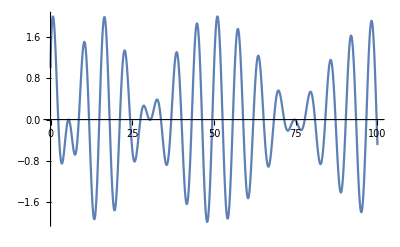

```mathematica
Plot[Sin[x+Sqrt[x]]+Cos[x-Sqrt[x]],{x,0,100}]
```

```mathematica
Limit[Sin[x+Sqrt[x]]+Cos[x-Sqrt[x]],x->Infinity]
```

Interval[{-4,4}]

```mathematica
MaxLimit[Sin[x+Sqrt[x]]+Cos[x-Sqrt[x]],x->Infinity]
```

max lim_(x→∞) (Cos[√x-x]+Sin[√x+x])

```mathematica
MaxLimit[Sin[x+Sqrt[2]]+Cos[x-Sqrt[3]],x->Infinity]
```

Cos[√3+2 ArcTan[(Cos[√3]+Sin[√2])/(Cos[√2]+Sin[√3])-(√(Cos[√2]^2+Cos[√3]^2+2 Cos[√3] Sin[√2]+Sin[√2]^2+2 Cos[√2] Sin[√3]+Sin[√3]^2))/(Cos[√2]+Sin[√3])]]+Sin[√2-2 ArcTan[(Cos[√3]+Sin[√2])/(Cos[√2]+Sin[√3])-(√(Cos[√2]^2+Cos[√3]^2+2 Cos[√3] Sin[√2]+Sin[√2]^2+2 Cos[√2] Sin[√3]+Sin[√3]^2))/(Cos[√2]+Sin[√3])]]

```mathematica
FullSimplify[%107]
```

Cos[√3+2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[√2+√3])))/(Cos[√2]+Sin[√3])]]+Sin[√2-2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[√2+√3])))/(Cos[√2]+Sin[√3])]]

```mathematica
N[%]
```

1.41091

```mathematica
N[%109,100]
```

1.410906304926814721428195305603506409856283025067460886423763925492163193932707469959998338983873344

```mathematica
RootReduce[%109]
```

Cos[√3+2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/(Cos[√2]+Sin[√3])]]+Sin[√2-2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/(Cos[√2]+Sin[√3])]]

```mathematica
TrigExpand[%]
```

Cos[√3]/(1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2)+Sin[√2]/(1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2)-(2 Cos[√3])/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-Cos[√3]^3/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Sin[√2])/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(3 Cos[√3]^2 Sin[√2])/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(3 Cos[√3] Sin[√2]^2)/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-Sin[√2]^3/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Cos[√2] Cos[√3])/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Cos[√2] Sin[√2])/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Cos[√3] Sin[√3])/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Sin[√2] Sin[√3])/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Cos[√3] Sin[Root[1-10 #1^2+#1^4&,4]])/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))-(2 Sin[√2] Sin[Root[1-10 #1^2+#1^4&,4]])/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))+(2 √2 Sin[√2]^2 √(1+Sin[Root[1-10 #1^2+#1^4&,4]]))/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))+(2 Cos[√3]^2 √(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))+(4 Cos[√3] Sin[√2] √(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/((Cos[√2]+Sin[√3])^2 (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))+(2 Cos[√2] √(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))+(2 Sin[√3] √(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))/((Cos[√2]+Sin[√3]) (1+((Cos[√3]+Sin[√2]-√(2 (1+Sin[Root[1-10 #1^2+#1^4&,4]])))^2)/(Cos[√2]+Sin[√3])^2))

```mathematica
FullSimplify[%]
```

√(2 (1+Sin[√2+√3]))

```mathematica
FullSimplify[%112]
```

Cos[√3+2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[√2+√3])))/(Cos[√2]+Sin[√3])]]+Sin[√2-2 ArcTan[(Cos[√3]+Sin[√2]-√(2 (1+Sin[√2+√3])))/(Cos[√2]+Sin[√3])]]

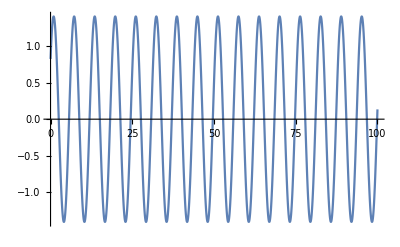

```mathematica
Plot[Sin[x+Sqrt[2]]+Cos[x-Sqrt[3]],{x,0,100}]
```

```mathematica
FullSimplify[f[a,b]==f[b,a],ForAll[{p,q,r},f[f[f[p,q],r],f[p,f[f[p,r],p]]]==r]]
```

True

```mathematica
ResourceData["Proof of Wolfram's Axiom for Boolean Algebra"]
```

Dataset[<>]

```mathematica
ResourceData["Proof of Wolfram's Axiom for Boolean Algebra"][All,"Statement"]
```

Dataset[<>]

```mathematica
Values[%]
```

Dataset[<>]

```mathematica
Take[%,5]
```

Dataset[<>]

```mathematica
Normal[%]
```

{((a·b)·c)·(a·((a·c)·a))==c,(a·((a·a)·a))·(a·((a·a)·a))==a,(a·a)·((a·((a·a)·a))·a)==a,(a·b)·((a·a)·(((a·a)·b)·(a·a)))==b,((a·((a·b)·a))·d)·(b·((b·d)·b))==d}

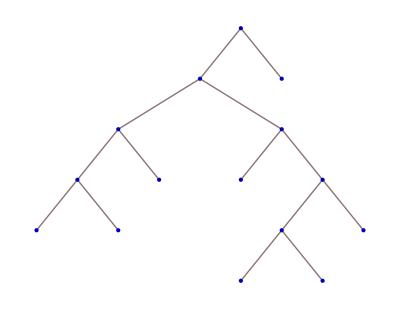
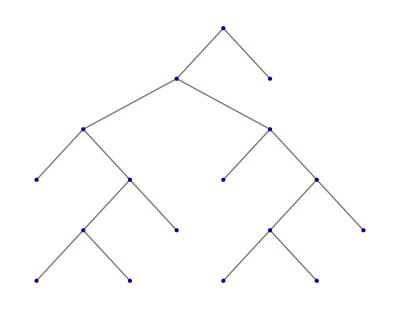
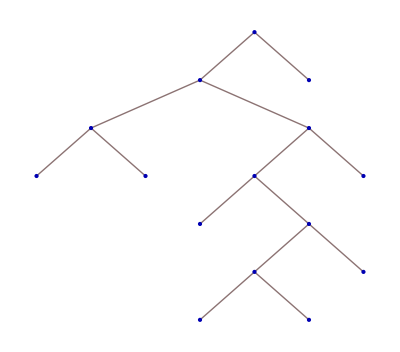
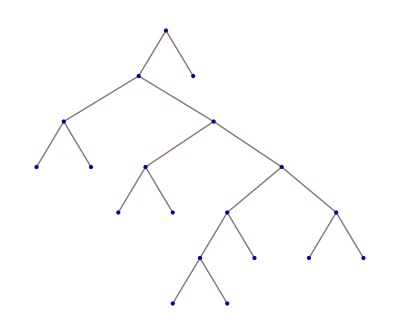
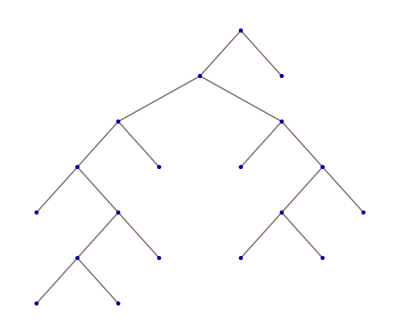

```mathematica
TreeForm[#,VertexLabeling->False]&/@%121
```

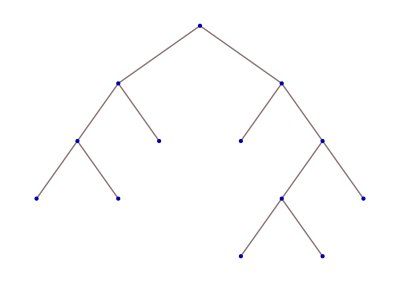
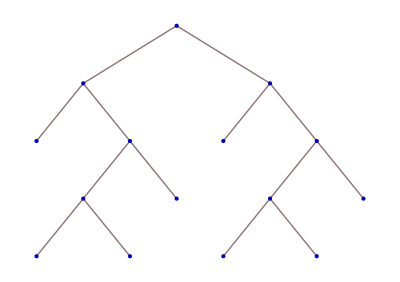
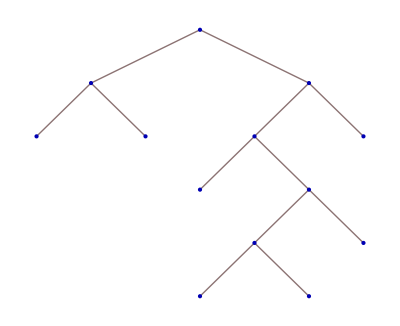
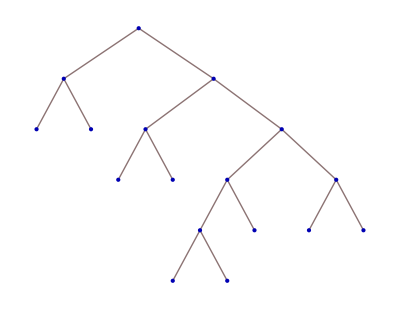
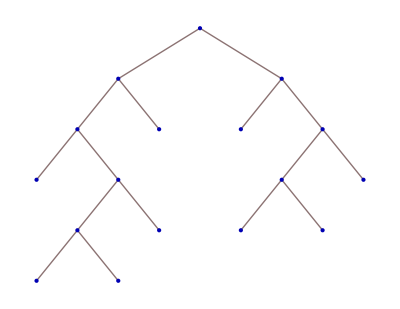
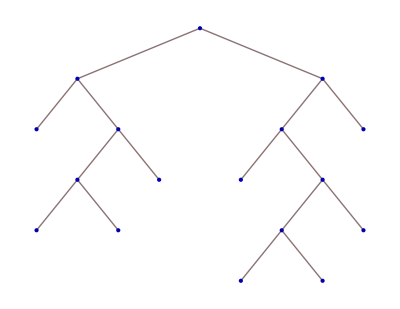
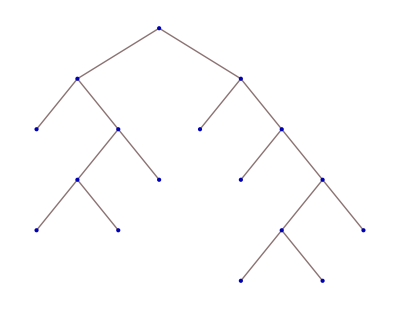
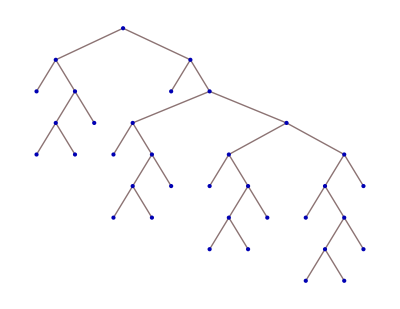
{-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-,-Graphics-==-Graphics-}

```mathematica
Map[TreeForm[#,VertexLabeling->False]&,Normal[%119],{2}]
```

```mathematica
ItoProcess
```

```mathematica
ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+x[t]^2)ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]]
```

```mathematica
Table[ListLinePlot[RandomFunction[WienerProcess[],{0,10,.1}]],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+x[t]^2)ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,10,.1}]],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Mean[ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+x[t]^2)ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]][t]]
```

ⅇ^-t

```mathematica
Kurtosis[ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+x[t]^2)ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]][t]]
```

(-3 ⅇ^(-4 t)+6 ⅇ^(-2 t)-4 ⅇ^(-2 t) (-3+4 ⅇ^t)+ⅇ^-t (-3 ⅇ^t+4 ⅇ^(3 t)))/((1-ⅇ^(-2 t))^2)

```mathematica
Plot[%,{t,0,10}]
```

-Graphics-

```mathematica
Histogram[RandomFunction[WienerProcess[],{0,1000,.1}]]
```

-Graphics-

```mathematica
Histogram[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+x[t]^2)ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,1000,.1}]]
```

-Graphics-

```mathematica
Histogram[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+√(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,1000,.1}]]
```

-Graphics-

```mathematica
Histogram[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+x[t] √(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,1000,.1}]]
```

-Graphics-

```mathematica
ListLinePlot[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+x[t] √(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,10,.1}]]
```

-Graphics-

```mathematica
ListLogPlot[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+x[t] √(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,10,.1}],Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+Sqrt[Abs[x[t]]] √(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,10,.1}],Joined->True]
```

-Graphics-

```mathematica
ListPlot[RandomFunction[ItoProcess[ⅆx[t]==-x[t]ⅆt+Sqrt[Abs[x[t]]] √(1+Abs[x[t]])ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],{0,10,.1}],Joined->True]
```

-Graphics-